# Moments

```mathematica
timepoint=130;
```

DBM - 1 layer - 3 species

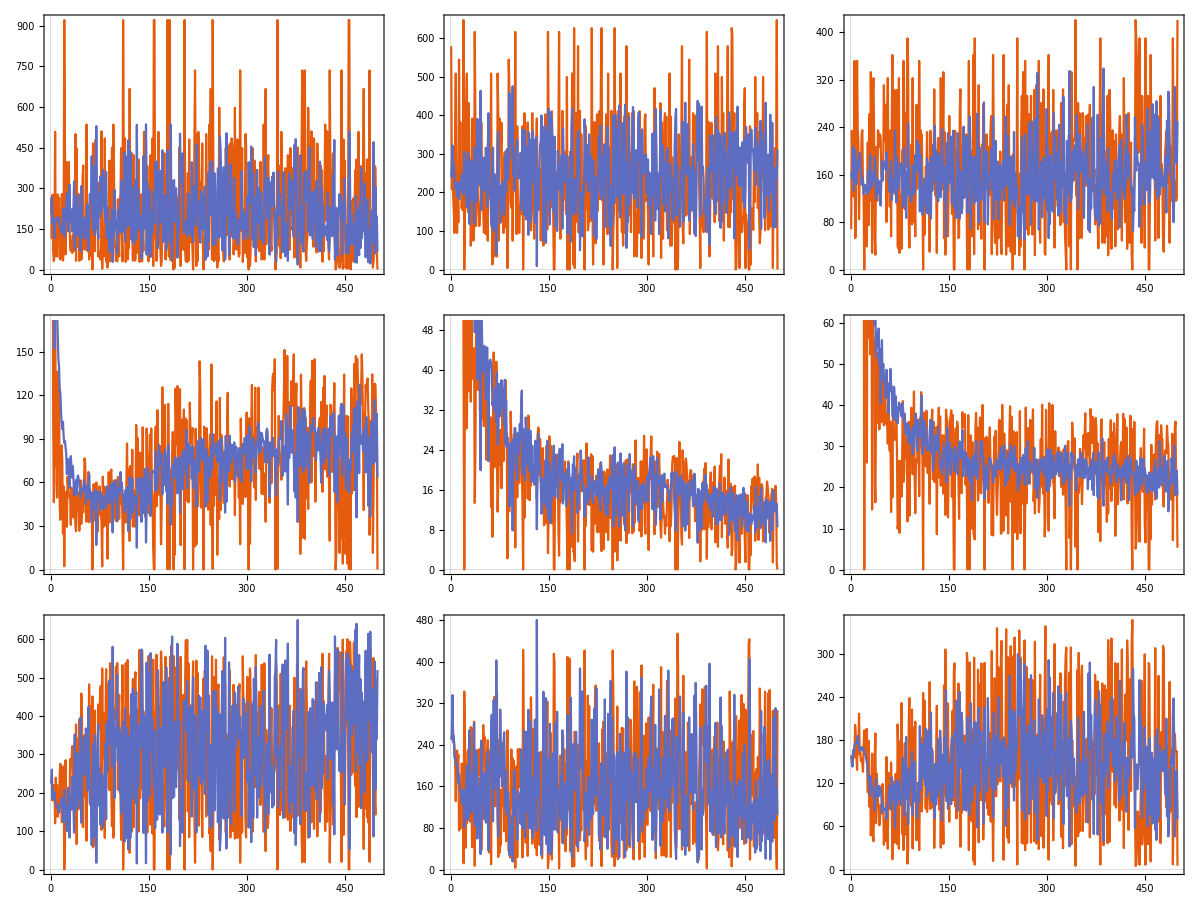

```mathematica
SetDirectory[NotebookDirectory[]];
dir="../data/fine_tune_1layers/"<>IntegerString[timepoint,10,4]<>"/moments/";
datahA=Transpose[Import[dir<>"hA.txt","Table"]];
datahB=Transpose[Import[dir<>"hB.txt","Table"]];
datahC=Transpose[Import[dir<>"hC.txt","Table"]];
datawAX1=Transpose[Import[dir<>"wAX1.txt","Table"]];
datawBY1=Transpose[Import[dir<>"wBY1.txt","Table"]];
datawCZ1=Transpose[Import[dir<>"wCZ1.txt","Table"]];
databX1=Transpose[Import[dir<>"bX1.txt","Table"]];
databY1=Transpose[Import[dir<>"bY1.txt","Table"]];
databZ1=Transpose[Import[dir<>"bZ1.txt","Table"]];

size=150;
Grid[{{ListLinePlot[datahA,ImageSize->size],ListLinePlot[datahB,ImageSize->size],ListLinePlot[datahC,ImageSize->size]
},{ListLinePlot[datawAX1,ImageSize->size],ListLinePlot[datawBY1,ImageSize->size],ListLinePlot[datawCZ1,ImageSize->size]
},{ListLinePlot[databX1,ImageSize->size],ListLinePlot[databY1,ImageSize->size],ListLinePlot[databZ1,ImageSize->size]
}}]
```

```mathematica
Mean[datahB[[2,-200;;]]]//N
```

253.625

DBM - 2 layers - 3 species

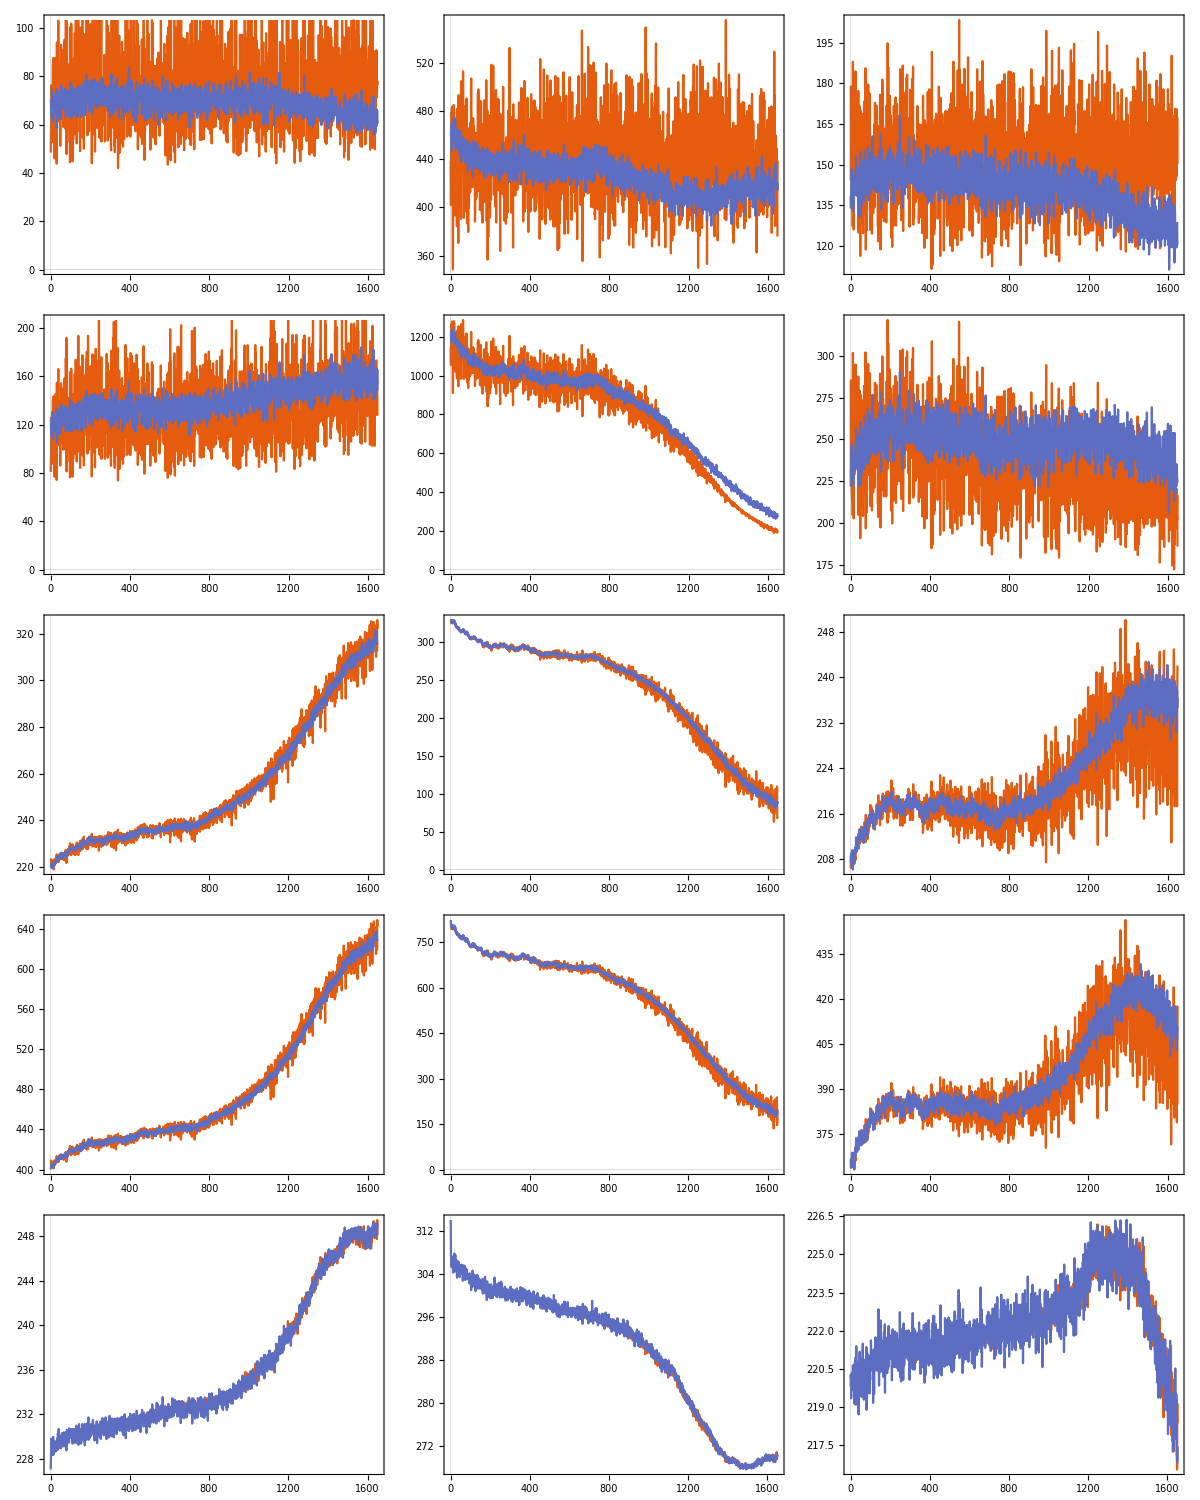

```mathematica
SetDirectory[NotebookDirectory[]];
dir="../data/fine_tune_2layers/"<>IntegerString[timepoint,10,4]<>"/moments/";
datahA=Transpose[Import[dir<>"hA.txt","Table"]];
datahB=Transpose[Import[dir<>"hB.txt","Table"]];
datahC=Transpose[Import[dir<>"hC.txt","Table"]];
datawAX1=Transpose[Import[dir<>"wAX1.txt","Table"]];
datawBY1=Transpose[Import[dir<>"wBY1.txt","Table"]];
datawCZ1=Transpose[Import[dir<>"wCZ1.txt","Table"]];
databX1=Transpose[Import[dir<>"bX1.txt","Table"]];
databY1=Transpose[Import[dir<>"bY1.txt","Table"]];
databZ1=Transpose[Import[dir<>"bZ1.txt","Table"]];
datawX1X2=Transpose[Import[dir<>"wX1X2.txt","Table"]];
datawY1Y2=Transpose[Import[dir<>"wY1Y2.txt","Table"]];
datawZ1Z2=Transpose[Import[dir<>"wZ1Z2.txt","Table"]];
databX2=Transpose[Import[dir<>"bX2.txt","Table"]];
databY2=Transpose[Import[dir<>"bY2.txt","Table"]];
databZ2=Transpose[Import[dir<>"bZ2.txt","Table"]];

size=150;
Grid[{{ListLinePlot[datahA,ImageSize->size],ListLinePlot[datahB,ImageSize->size],ListLinePlot[datahC,ImageSize->size]
},{ListLinePlot[datawAX1,ImageSize->size],ListLinePlot[datawBY1,ImageSize->size],ListLinePlot[datawCZ1,ImageSize->size]
},{ListLinePlot[databX1,ImageSize->size],ListLinePlot[databY1,ImageSize->size],ListLinePlot[databZ1,ImageSize->size]
},{ListLinePlot[datawX1X2,ImageSize->size],ListLinePlot[datawY1Y2,ImageSize->size],ListLinePlot[datawZ1Z2,ImageSize->size]
},{ListLinePlot[databX2,ImageSize->size],ListLinePlot[databY2,ImageSize->size],ListLinePlot[databZ2,ImageSize->size]
}}]
```